CustomTicks package
Mark A. Caprio, Department of Physics, University of Notre Dame
Version 2.1.1 (August 26, 2020)

Notebook notes:
	StyleSheet is HelpBrowser.
	Notebook options: "Cell Options">>"Display Options">>"Cell Element Spacings">>"ClosedCellHeight"->1
	Hyphenation: LanguageCategory set to None is supposed to prevent hyphenation but does not seem to work as advertised.  Setting Hyphenation to None also fails.  Each cell's Hyphenation option must be set to None.
	Before distribution: update version number in footer, convert all -> to → in running text; set AppendTo directory argument to c:\\example, select all cells and set "Formatting Options">>"Text Layout">>Hyphenation to None; unset options Editable and Deletable
	
	Initialization:
	Get[“LevelScheme`MCText`”]

#### Introduction

Mathematica provides a powerful system for generating graphics but does not provide, in built-in form, the fine formatting control necessary for the preparation of publication quality figures.  The CustomTicks package provides detailed customization of tick mark placement and formatting.  The flexibility achieved matches or exceeds that available with most commercial scientific plotting software.  Linear, logarithmic, and general nonlinear axes are supported.  Some tick mark manipulation functions, for use in graphics programming, are also provided by the CustomTicks package.

The CustomTicks package is part of the SciDraw system for preparing publication-quality scientific figures with Mathematica (http://scidraw.nd.edu).  It was originally developed as part of LevelScheme [Comput. Phys. Commun. 171, 107 (2005)].

#### Basic use for linear axes

The default tick marks produced by Mathematica's plotting functions are typically not ideal for publication.  It is often desirable to be able to change the tick spacing from that selected by Mathematica.  The tick marks are also often too short to be easily visible.

It is possible to override the default Mathematica ticks by specifying a list of tick marks, complete with formatting information, as the value for the Ticks or FrameTicks option (see the Mathematica documentation for basic plotting options).  It is prohibitively tedious to construct such lists by hand.  The CustomTicks package provides functions to automatically construct lists of tick marks, with detailed control over formatting.

```mathematica
MakeHelpBox["SymbolSummary",


{texttt["LinTicks["],textit["x1"],texttt[","],textit["x2"],texttt["]"]},
{"Produces linear tick specifications, with automatically chosen major and minor tick intervals"},

{texttt["LinTicks["],textit["x1"],texttt[","],textit["x2"],texttt[","],textit["interval"],texttt[","],textit["subdivs"],texttt["]"]},
{"Produces linear tick specifications, with manually chosen major and minor tick intervals"}



];
MakeCaptionBox[{"Tick specification function."}];
MakeHelpBox["OptionSummaryWideDescription",


{texttt["TickRange"]},{texttt["{-Infinity,Infinity}"]},{"Limits the drawing of ticks (and their labels) to given coordinate range"},
{texttt["ShowMinorTicks"]},{texttt["True"]},{"Controls whether or not the minor ticks are drawn; mainly for use with ", texttt["LogTicks"]," (see below)"}


];
MakeCaptionBox[{"Options controlling the coordinates at which tick marks are displayed."}];
MakeHelpBox["OptionSummaryWideDescription",
{texttt["ShowTickLabels"]},{texttt["True"]},{"Controls whether or not major tick labels are printed"},

{texttt["ShowMinorTickLabels"]},{texttt["True"]},{"Controls whether or not minor tick labels are printed"},

{texttt["TickLabelRange"]},{texttt["{-Infinity,Infinity}"]},{"Limits printing of major tick labels to given coordinate range"},

{texttt["ShowFirst"]},{texttt["True"]},{"Controls whether or not first major tick label is printed"},

{texttt["ShowLast"]},{texttt["True"]},{"Controls whether or not last major tick label is printed"},


{texttt["TickLabelStep"]},{texttt["1"]},{"Limits printing of major tick labels to one in every ", texttt["TickLabelStep"]," major ticks"},

{texttt["TickLabelStart"]},{texttt["0"]},{"Used in conjunction with ", texttt["TickLabelStep"]," chooses which subset of major tick labels are printed"}
];
MakeCaptionBox[{"Options controlling which tick marks are accompanied by labels."}];

MakeHelpBox["OptionSummaryWideDescription",
{texttt["MajorTickLength"]},{texttt["0.01"]},{"Length for the major ticks (may also be given as a list of two lengths, into and out of the frame, as described in the Mathematica documentation for ",texttt["Ticks"],")"},

{texttt["MinorTickLength"]},{texttt["0.005"]},{"Length for the minor ticks (may also be given as a list of two lengths, into and out of the frame, as described in the Mathematica documentation for ",texttt["Ticks"],")"},

{texttt["TickDirection"]},{texttt["In"]},{"Orientation of tick marks (",texttt["In"]," for tick marks into the frame, ",texttt["Out"],"for tick marks out of the frame, or ",texttt["All"],"for tick marks both into and out of the frame)"},

{texttt["TickLengthScale"]},{texttt["1"]},{"Additional scale factor by which to lengthen both the major and minor ticks, relative to the lengths given by the options ",texttt["MajorTickLength"]," and ",texttt["MinorTickLength"]," above"},

{texttt["MajorTickStyle"]},{texttt["{}"]},{"List specifying the line style for the major ticks"},

{texttt["MinorTickStyle"]},{texttt["{}"]},{"List specifying the line style for the minor ticks"}

];
MakeCaptionBox[{"Options specifying the appearance of tick marks."}];

MakeHelpBox["OptionSummaryWideDescription",

{texttt["DecimalDigits"]},{texttt["Automatic"]},
{"Sets number of digits after decimal place for major tick labels; if ",texttt["Automatic"],", the maximum number of digits needed for any label is used for all labels"},

{texttt["NumberSigns"]},{texttt["Automatic"]},
{"Strings to use as signs for negative and positive numbers; see ",textit["Mathematica"],"documentation and discussion of ",texttt["FixedPointForm"]," function below"},


{texttt["NumberPoint"]},{texttt["\".\""]},
{"String to use as decimal point"}


];
MakeCaptionBox[{"Options specifying the numerical formatting of tick labels (if the default labeling function is used)."}];
```

LinTicks[x1,x2] | Produces linear tick specifications, with automatically chosen major and minor tick intervals
LinTicks[x1,x2,interval,subdivs] | Produces linear tick specifications, with manually chosen major and minor tick intervals

Tick specification function.

option name | default value | 
TickRange | {-Infinity,Infinity} | Limits the drawing of ticks (and their labels) to given coordinate range
ShowMinorTicks | True | Controls whether or not the minor ticks are drawn; mainly for use with LogTicks (see below)

Options controlling the coordinates at which tick marks are displayed.

option name | default value | 
ShowTickLabels | True | Controls whether or not major tick labels are printed
ShowMinorTickLabels | True | Controls whether or not minor tick labels are printed
TickLabelRange | {-Infinity,Infinity} | Limits printing of major tick labels to given coordinate range
ShowFirst | True | Controls whether or not first major tick label is printed
ShowLast | True | Controls whether or not last major tick label is printed
TickLabelStep | 1 | Limits printing of major tick labels to one in every TickLabelStep major ticks
TickLabelStart | 0 | Used in conjunction with TickLabelStep chooses which subset of major tick labels are printed

Options controlling which tick marks are accompanied by labels.

option name | default value | 
MajorTickLength | 0.01 | Length for the major ticks (may also be given as a list of two lengths, into and out of the frame, as described in the Mathematica documentation for Ticks)
MinorTickLength | 0.005 | Length for the minor ticks (may also be given as a list of two lengths, into and out of the frame, as described in the Mathematica documentation for Ticks)
TickDirection | In | Orientation of tick marks (In for tick marks into the frame, Outfor tick marks out of the frame, or Allfor tick marks both into and out of the frame)
TickLengthScale | 1 | Additional scale factor by which to lengthen both the major and minor ticks, relative to the lengths given by the options MajorTickLength and MinorTickLength above
MajorTickStyle | {} | List specifying the line style for the major ticks
MinorTickStyle | {} | List specifying the line style for the minor ticks

Options specifying the appearance of tick marks.

option name | default value | 
DecimalDigits | Automatic | Sets number of digits after decimal place for major tick labels; if Automatic, the maximum number of digits needed for any label is used for all labels
NumberSigns | Automatic | Strings to use as signs for negative and positive numbers; see Mathematicadocumentation and discussion of FixedPointForm function below
NumberPoint | "." | String to use as decimal point

Options specifying the numerical formatting of tick labels (if the default labeling function is used).

#### Logarithmic axes

The function LogTicks generates tick marks for logarithmic axes.  LogTicks can produce tick marks for an arbitrary logarithmic base (10 is the default, but e and 2 are other commonly useful bases).  Unlike the Mathematica LogPlot function, which produces cumbersome decimal labels (e.g., "0.0000001", "0.000001", …), LogTicks produces true exponential labels (e.g., "10^-7", "10^-6", …).

```mathematica
MakeHelpBox["SymbolSummary",

{texttt["LogTicks["],textit["n1"],texttt[","],textit["n2"],texttt["]"]},
{"Produces logarithmic tick specifications, base 10"},

{texttt["LogTicks["],textit["base"],texttt[","],textit["n1"],texttt[","],textit["n2"],texttt["]"]},
{"Produces logarithmic tick specifications, arbitrary ",textit["base"]}



];
MakeCaptionBox[{"Logarithmic tick specification function."}];
```

LogTicks[n1,n2] | Produces logarithmic tick specifications, base 10
LogTicks[base,n1,n2] | Produces logarithmic tick specifications, arbitrary base

Logarithmic tick specification function.

LogTicks must be given the starting power, ending power, and, optionally, the logarithmic base b.  For base 10, a total of eight minor ticks are produced in each major interval, at 2×10^n through 9×10^n.  For an arbitrary base b, ⌈b⌉-2 minor ticks are produced, at 2×b^n, 3×b^n, ….  Display of the minor ticks may be suppressed by specifying the option ShowMinorTicks→False.  Some examples are shown below.

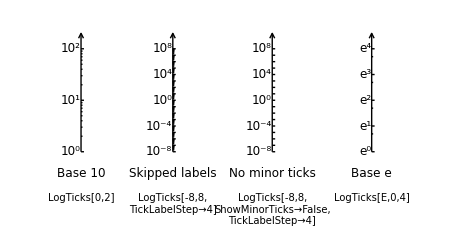

```mathematica
Scheme[
{
CodeOpts={FontFamily->"Courier",FontSize->10},
SetOptions[ManualLabel,Offset->{0,+1}],

SetOrigin[1],
SchemeAxis[Left,0,{0,2.3},Ticks->LogTicks[0,2]],
ManualLabel[{0,-0.3},StackText[Center,0.5,{"Base 10"}]],
ManualLabel[{0,-0.8},"LogTicks[0,2]",CodeOpts],

SetOrigin[2.2],
SchemeAxis[Left,0,{0,2.3},Ticks->LogTicks[-8,8,TickLabelStep->4,TickPostTransformation->((#/8+1)&)]],
ManualLabel[{0,-0.3},StackText[Center,0.5,{"Skipped labels"}]],
ManualLabel[{0,-0.8},StackText[Center,0,{"LogTicks[-8,8,","TickLabelStep→4]"}],CodeOpts],

SetOrigin[3.5],
SchemeAxis[Left,0,{0,2.3},Ticks->LogTicks[-8,8,ShowMinorTicks->False,TickLabelStep->4,TickPostTransformation->((#/8+1)&)]],
ManualLabel[{0,-0.3},StackText[Center,0.5,{"No minor ticks"}]],
ManualLabel[{0,-0.8},StackText[Center,0,{"LogTicks[-8,8,","ShowMinorTicks→False,","TickLabelStep→4]"}],CodeOpts],


SetOrigin[4.8],
SchemeAxis[Left,0,{0,2.3},Ticks->LogTicks[E,0,4,TickPostTransformation->((#/2)&)]],
ManualLabel[{0,-0.3},RowBox[{"Base ",textit["e"]}]],
ManualLabel[{0,-0.8},"LogTicks[E,0,4]",CodeOpts],


},
PlotRange->{{0.5,5.5},{-1.5,2.5}},ImageSize->72*{6.5,3.5}
]
```

This tick function was designed on the assumption that you will be generating your plots with logarithmic axes the “manual” way.  That is, as far as the plotting functions are concerned, you are actually generating linear plots, but you have taken the logarithm of either the x-axis or y-axis variable.  Specifically, for base 10,
	(1) a logarithmic (or linear-log) plot of f is obtained by plotting log_10 f(x), 
	(2) a log-linear plot of f is obtained by plotting f(10^x), and
	(3) a log-log plot of f is obtained by plotting log_10 f(10^x)
on ordinary linear axes.  A similar procedure holds for bases other than 10.  Examples of a logarithmic plot and a log-log plot follow.

Plot[
    {Log10[Cosh[x]],Log10[Sinh[x]]},{x,0,10},
    PlotRange→{{-0.0001,4},{-0.5,2.5}},
    FrameTicks→{
        {LogTicks[10,-1,3],LogTicks[10,-1,3,ShowTickLabels→False]},
        {LinTicks[0,4],LinTicks[0,4,ShowTickLabels→False]}
        },
    Axes→False,Frame→True,ImageSize→72*3
    ]

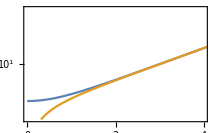

```mathematica
Plot[
{Log10[Cosh[x]],Log10[Sinh[x]]},{x,0,10},
PlotRange->{{-0.0001,4},{-0.5,2.5}},
FrameTicks->{
{LogTicks[10,-1,3],LogTicks[10,-1,3,ShowTickLabels->False]},{LinTicks[0,4],LinTicks[0,4,ShowTickLabels->False]}
},
Axes->False,Frame->True,ImageSize->72*3
]
```

Plot[
    {Log10[(10^x)^2],Log10[(10^x)^5]},{x,-1,3},
    PlotRange→{{-0.0001,3},{-0.5,4.5}},
    FrameTicks→{
        {LogTicks[10,-1,5],None},
        {LogTicks[10,0,3],None}
        },
    Axes→False,Frame→True,ImageSize→72*3
    ]

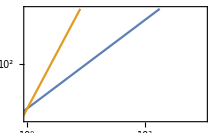

```mathematica
Plot[
{Log[10,(10^x)^2],Log[10,(10^x)^5]},{x,-1,3},
PlotRange->{{-0.0001,3},{-0.5,4.5}},
FrameTicks->{
{LogTicks[10,-1,5],None},{LogTicks[10,0,3],None}
},
Axes->False,Frame->True,ImageSize->72*3,BaseStyle->{FontFamily->"Times"}
]
```

If, instead, you wish to use LogPlot or related Mathematica functions directly for your logarithmic plots, see the discussion below, under “Use with LogPlot and related functions”.

#### Automatic ticks for Mathematica plot functions

The functions LinTicks and LogTicks can also be specified as automatic tick generation functions for the Mathematica plotting functions.  This saves you typing the plot range explicitly each time, at least if you do not wish to specify details such as the number of subdivisions.

Plot[
    {Log10[Cosh[x]],Log10[Sinh[x]]},{x,0,10},
    PlotRange→{{-0.0001,4},{-0.5,2.5}},
    FrameTicks→{{LogTicks,None},{LinTicks,None}},
    Axes→False,Frame→True,ImageSize→72*3
    ]

```mathematica
Plot[
{Log[10,Cosh[x]],Log[10,Sinh[x]]},{x,0,10},
PlotRange->{{-0.0001,4},{-0.5,2.5}},
FrameTicks->{{LogTicks,None},{LinTicks,None}},
Axes->False,Frame->True,ImageSize->72*3,BaseStyle->{FontFamily->"Times"}
]
```

-Graphics-

What if you wish to have tick marks on the top and right as well, but without labels on them?  Simply specifying FrameTicks→{LinTicks,LogTicks} or FrameTicks→{LinTicks,LogTicks,LinTicks,LogTicks} would unfortunately result in ticks with unsightly and redundant labels.  This can be avoided with the CustomTicks StripTickLabels wrapper function, as shown below.

Plot[
    {Log10[Cosh[x]],Log10[Sinh[x]]},{x,0,10},
    PlotRange→{{-0.0001,4},{-0.5,2.5}},
    FrameTicks→{{LogTicks,StripTickLabels[LogTicks]},{LinTicks,StripTickLabels[LinTicks]}},
    Axes→False,Frame→True,ImageSize→72*3
    ]

```mathematica
Plot[
{Log[10,Cosh[x]],Log[10,Sinh[x]]},{x,0,10},
PlotRange->{{-0.0001,4},{-0.5,2.5}},
FrameTicks->{{LogTicks,StripTickLabels[LogTicks]},{LinTicks,StripTickLabels[LinTicks]}},
Axes->False,Frame->True,ImageSize->72*3,BaseStyle->{FontFamily->"Times"}
]
```

-Graphics-

If you are doing many such plots, it is easiest to set the necessary options as the default options for Plot.

SetOptions[
  Plot,
  Axes→False,Frame→True,
  FrameTicks→{{LogTicks,StripTickLabels[LogTicks]},{LinTicks,StripTickLabels[LinTicks]}}
];
GraphicsGrid[{{Plot[Log10[x^2],{x,0,10}],Plot[Log10[x^-2],{x,0,10}]}}]

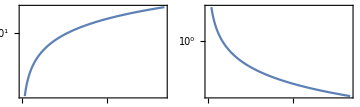

```mathematica
SetOptions[Plot,Axes->False,Frame->True,FrameTicks->{{LogTicks,StripTickLabels[LogTicks]},{LinTicks,StripTickLabels[LinTicks]}},BaseStyle->{FontFamily->"Times"}];
GraphicsGrid[{{Plot[Log[10,x^2],{x,0,10}],Plot[Log[10,x^-2],{x,0,10}]}},
ImageSize->5*72]
```

```mathematica
MakeHelpBox["OptionSummaryWideDescription",


{texttt["LogPlot"]},{texttt["False"]},{"Controls whether ",texttt["LogTicks"],"operates as it should for standalone use or for automatic tick mark generation with Mathematica's ",texttt["LogPlot"]}


];
MakeCaptionBox[{texttt["LogTicks"]," special option."}];
```

option name | default value | 
LogPlot | False | Controls whether LogTicksoperates as it should for standalone use or for automatic tick mark generation with Mathematica's LogPlot

LogTicks special option.

#### Use with LogPlot and related functions

If you wish to use LogPlot or related Mathematica functions directly for your logarithmic plots, you may also do so.  However, LogTicks must then be instructed to adjust its output accordingly.  (LogPlot expects tick coordinates to be specified as the true coordinate value, not the logarithm of the coordinate value.  LogTicks must also interpret its n1 and n2 arguments differently in this case.)  Automatic use with LogPlot can be accomplished by setting the option LogPlot->True.

SetOptions[LogTicks, LogPlot -> True];
Plot[
 {Cosh[x], Sinh[x]}, {x, 0, 10},
 PlotRange->{{-0.0001, 4},{10^-0.5, 10^2.5}},
 FrameTicks->{{LogTicks,StripTickLabels[LogTicks]},{LinTicks,StripTickLabels[LinTicks]}},
 Frame->True, ImageSize -> 72*3
 ]

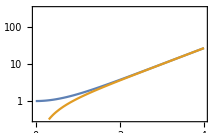

```mathematica
SetOptions[LogTicks,LogPlot->True];
LogPlot[
{Cosh[x],Sinh[x]},{x,0,4},
PlotRange->{{-0.0001,4},{10^-0.5,10^2.5}},
FrameTicks->{{LogTicks,StripTickLabels[LogTicks]},{LinTicks,StripTickLabels[LinTicks]}},
Frame->True,ImageSize->72*3
]
```

Alternatively, if you are a SciDraw user, you might find  yourself wanting to include the output of Mathematica’s LogPlot in a SciDraw figure, via FigGraphics, and then put logarithmic ticks on this figure.  (I generally just use the manual approach above, instead, and do not bother with LogPlot.  But you may be a diehard LogPlot user...)
	Similarly, if you are a more advanced Mathematica graphics programmer, you might find yourself wishing to use LogPlot or related Mathematica functions to generate graphics which you will then combine with other graphics to form a composite figure, and you then may wish to put logarithmic ticks on this figure.  It turns out that LogPlot and its ilk do essentially what we described as the manual procedure above.  That is, they generate linear plots in which they have taken the logarithms of the coordinates.  But, they actually take the logarithm base e, rather than base 10.  (No matter that the ticks which they generate by default are base 10 log ticks...)  So, if you create ticks with LogTicks, the coordinates describing where these ticks should be placed must be adjusted accordingly.  For instance, the tick for “10”, instead of being located at log_1010=1 according to the procedure we described before, must now be at log_e10≈2.30259.  This rescaling of coordinates may be accomplished with the option setting LogPlot->E.  Technical note: This option has the same effect as TickPostTransformation→(Log[10]*#&) (see below).

#### Further control over tick placement and advanced customization

```mathematica
TmpMakeHelpBox["OptionSummaryWideDescription",Contents___List]:=MakeColumnBox["3ColumnBox",3,{ColumnAlignments->{Left},RowLines->{True,False},RowSpacings->1.5,ColumnWidths->{0.28,0.18,0.5}},
{StyleBox["option name","SO10"]},{StyleBox["default value","SO10"]},{""},
Contents];
TmpMakeHelpBox["OptionSummaryWideDescription",

{texttt["TickLabelFunction"]},{texttt["Automatic"]},{"Function used to generate major tick labels (first argument is the numerical coordinate, second argument is the ",texttt["LinTicks"]," default formatted label); ",texttt["Automatic"]," gives the default label"},

{texttt["TickPreTransformation"]},{texttt["Identity"]},{"Function to be applied to tick coordinates, before range tests and label generation"},

{texttt["TickPostTransformation"]},{texttt["Identity"]},{"Function to be applied to tick coordinates, after range tests and label generation"},

{texttt["MinorTickIndexTransformation"]},{texttt["Identity"]},{"Function to be applied to minor tick indices (originally 1, 2, …, ",textit["subdivs"],"-1) before minor tick coordinate is obtained by linear interpolation between major tick positions"},

{texttt["MinorTickIndexRange"]},{texttt["{1,Infinity}"]},{"Limits drawing of minor ticks to those with indices (before tranformation) in given range"},

{texttt["MinorTickLabelStyle"]},{texttt["None"]},{"Text style for minor tick labels"}

];
MakeCaptionBox[{"Advanced customization options."}];
```

option name | default value | 
TickLabelFunction | Automatic | Function used to generate major tick labels (first argument is the numerical coordinate, second argument is the LinTicks default formatted label); Automatic gives the default label
TickPreTransformation | Identity | Function to be applied to tick coordinates, before range tests and label generation
TickPostTransformation | Identity | Function to be applied to tick coordinates, after range tests and label generation
MinorTickIndexTransformation | Identity | Function to be applied to minor tick indices (originally 1, 2, …, subdivs-1) before minor tick coordinate is obtained by linear interpolation between major tick positions
MinorTickIndexRange | {1,Infinity} | Limits drawing of minor ticks to those with indices (before tranformation) in given range
MinorTickLabelStyle | None | Text style for minor tick labels

Advanced customization options.

LinTicks accepts several options for advanced customization, allowing fully customizable labels and general nonlinear axis scales.  The option TickLabelFunction is used to specify the function to be used to construct tick labels (see the Mathematica documentation for Function for information on defining functions).  The label function is given as arguments both the raw numerical tick coordinate and the LinTicks default formatted label, so it can work with whichever is more convenient.  The label function may be used for simple tasks, such as attaching a prefix or suffix to the usual default label, or for more sophisticated formatting.  In the following example, tick values are formatted as rational multiples of π.

LinTicks[0,2*Pi,Pi/2,4,TickLabelFunction→(Rationalize[#/Pi]*Pi&)]

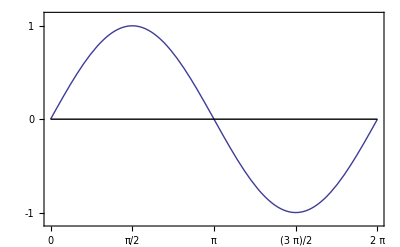

```mathematica
Scheme[
{
RawGraphics[Plot[Sin[x],{x,0,2*Pi},DisplayFunction->Identity]],
SchemeLine[{{0,0},{2*Pi,0}}]
},
PlotRange->{{0,2*Pi},{-1.1,1.1}},
Frame->True,FrameTicks->{LinTicks[0,2*Pi,Pi/2,4,TickLabelFunction->(Rationalize[#/Pi]*Pi&)],LinTicks[-2,2,1,5],None,None}
]
```

Nonlinear axes are constructed using the coordinate transformation functions.  For instance, the LogTicks function provided by the CustomTicks package is actually implemented as a special case of LinTicks, with transformed minor tick positions.  A very simplified implementation of LogTicks (base 10 logarithm only) is given below for illustration.

Log10Ticks[p1_Integer,p2_Integer,Opts___?OptionQ]:=LinTicks[
	  p1,p2,1,9,
      TickLabelFunction→(DisplayForm[SuperscriptBox[10,IntegerPart[#]]]&),
      MinorTickIndexTransformation→(Log10[#+1]*9&),
      Opts
      ];

```mathematica
MakeHelpBox["SymbolSummary",


{texttt["LinTicks["],textit["majorticklist"],texttt[","],textit["minorticklist"],texttt["]"]},
{"Produces major and minor ticks at the specified coordinate values"}

];
MakeCaptionBox[{"Form of tick specification function for ticks at arbitrary locations."}];
```

LinTicks[majorticklist,minorticklist] | Produces major and minor ticks at the specified coordinate values

Form of tick specification function for ticks at arbitrary locations.

Ticks may be placed at arbitrary coordinate locations by using the most flexible form of LinTicks, in which all major and minor tick coordinates are specified explicitly in two lists.  All the usual coordinate-transformation and customization options described above (except MinorTickIndexRange) are still applicable.

```mathematica
Scheme[
{
CodeOpts={FontFamily->"Courier",FontSize->10},
SetOptions[ManualLabel,Offset->{0,+1}],

SchemeAxis[Bottom,{0,6.8},0,Ticks->LinTicks[{0,1,2,3,5},Range[0.1,0.9,0.1],MajorTickLength->4*0.00625 ,MinorTickLength->4*0.00375]],
ManualLabel[{3,-0.2-0.3},StackText[Center,0.5,{"Manual choice of tick coordinates"}]],
ManualLabel[{3,-0.2-0.8},"LinTicks[{0,1,2,3,5},Range[0.1,0.9,0.1]]",CodeOpts],


},
PlotRange->{{-1.5,7.5},{-1.5,0.5}},ImageSize->72*{5,1}
]
```

-Graphics-

```mathematica
MakeHelpBox["OptionSummaryWideDescription",
{texttt["ExtraTicks"]},{texttt["{}"]},{"Additional coordinate values at which to insert tick marks"},

{texttt["TickTest"]},{texttt["(True&)"]},{"Logical test  to be applied to coordinate values, to select the coordinates at which tick marks are displayed (provides further control beyond the simple range test provided by ",texttt["TickRange"]," above)"},

{texttt["TickLabelTest"]},{texttt["(True&)"]},{"Logical test to be applied to coordinate values, to select the coordinates at which tick labels are displayed (provides further control beyond the simple range test provided by ",texttt["TickLabelRange"]," above)"}


];
MakeCaptionBox[{"Further options controlling the placement of tick marks and labels."}];
```

option name | default value | 
ExtraTicks | {} | Additional coordinate values at which to insert tick marks
TickTest | (True&) | Logical test  to be applied to coordinate values, to select the coordinates at which tick marks are displayed (provides further control beyond the simple range test provided by TickRange above)
TickLabelTest | (True&) | Logical test to be applied to coordinate values, to select the coordinates at which tick labels are displayed (provides further control beyond the simple range test provided by TickLabelRange above)

Further options controlling the placement of tick marks and labels.

Or, even without taking complete manual control of the choice of tick positions, some further control over tick placement is provided through the options above.

#### Tick mark programming utilities

```mathematica
MakeHelpBox["SymbolSummary",


{texttt["LimitTickRange[{"],textit["x1"],texttt[","],textit["x2"],texttt["},"],textit["ticks"],texttt["]"]},
{"Selects those tick mark with coordinates in the range specified; approximate equality testing is used to avoid dropping ticks at the ends of the interval due to roundoff; ticks must be specifies as lists rather than bare numbers"},

{texttt["TransformTicks["],textit["coordfcn"],texttt[","],textit["lengthfcn"],texttt[","],textit["ticks"],texttt["]"]},
{"Applies the specified transformation functions to the tick coordinates and tick lengths, respectively; ticks must be specified with an explicit pair of in and out lengths"},

{texttt["StripTickLabels["],textit["ticks"],texttt["]"]},
{"Removes any text labels from ticks; ticks must be specified as lists rather than bare numbers"},

{texttt["AugmentTicks["],textit["labelfcn"],texttt[",{"],textit["l1"],texttt[","],textit["l2"],texttt["},"],textit["stylelist"],texttt[","],textit["ticks"],texttt["]"]},
{"Upgrades all tick specifications to full specifications, complete with labels, lengths into and out of the frame (default 0 for out), and style directives"},

{texttt["AugmentAxisTickOptions["],textit["numaxes"],texttt[","],textit["tickoptions"],texttt["]"]},
{"Given a list of tick options (themselves lists of tick specifications) for several axes, replaces any ",texttt["None"]," entries with null lists and appends additional null lists as needed to make ",textit["numaxes"]," entries; a value ",texttt["None"]," for ",textit["tickoptions"]," is replaced by a list of null lists"},

{texttt["TickQ["],textit["x"],texttt["]"]},
{"Tests whether or not ",textit["x"]," is a valid tick mark specificiation"},

{texttt["TickListQ["],textit["x"],texttt["]"]},
{"Tests whether or not ",textit["x"]," is a list of valid tick mark specificiations"}

];
MakeCaptionBox[{"Tick manipulation utilities."}];
```

LimitTickRange[{x1,x2},ticks] | Selects those tick mark with coordinates in the range specified; approximate equality testing is used to avoid dropping ticks at the ends of the interval due to roundoff; ticks must be specifies as lists rather than bare numbers
TransformTicks[coordfcn,lengthfcn,ticks] | Applies the specified transformation functions to the tick coordinates and tick lengths, respectively; ticks must be specified with an explicit pair of in and out lengths
StripTickLabels[ticks] | Removes any text labels from ticks; ticks must be specified as lists rather than bare numbers
AugmentTicks[labelfcn,{l1,l2},stylelist,ticks] | Upgrades all tick specifications to full specifications, complete with labels, lengths into and out of the frame (default 0 for out), and style directives
AugmentAxisTickOptions[numaxes,tickoptions] | Given a list of tick options (themselves lists of tick specifications) for several axes, replaces any None entries with null lists and appends additional null lists as needed to make numaxes entries; a value None for tickoptions is replaced by a list of null lists
TickQ[x] | Tests whether or not x is a valid tick mark specificiation
TickListQ[x] | Tests whether or not x is a list of valid tick mark specificiations

Tick manipulation utilities.

Several utility functions for tick mark manipulation and testing are provided.  These are mainly intended for use in graphics programming rather than for direct use by someone wishing to specify tick marks.  They are used internally by the LevelScheme figure preparation system.

```mathematica
MakeHelpBox["SymbolSummary",


{texttt["FractionDigits["],textit["x"],texttt["]"]},
{"Returns the number of digits to the right of the point in the decimal representation of ",textit["x"]}

];
MakeCaptionBox[{"Decimal digit counting function."}];
```

FractionDigits[x] | Returns the number of digits to the right of the point in the decimal representation of x

Decimal digit counting function.

FractionDigits determines the number of digits to the right of the point in the decimal representation of a number.  It is of use in constructing fixed-point tick labels.  It will, naturally, return large values, determined by Mathematica's Precision, for some numbers,  such as non-terminating rationals.  It accepts the option FractionDigitsBase, by default 10, for work with non-decimal representations.  Some examples follow:

```mathematica
FractionDigits[100]
FractionDigits[1.25]
FractionDigits[1/3]
```

0

2

17

```mathematica
MakeHelpBox["SymbolSummary",


{texttt["FixedPointForm["],textit["x"],texttt[","],textit["r"],texttt["]"]},
{"Formats ",textit["x"]," as a fixed–point number with ", textit["r"],"digits to the right of the decimal point."},
{texttt["FixedPointForm["],textit["x"],texttt[",{"],textit["l"],texttt[","],textit["r"],texttt["}]"]},
{"Formats ",textit["x"]," as a fixed–point number with ",textit["l"]," digits (or spaces) to the left and ", textit["r"]," digits to the right of the decimal point."}


];
MakeCaptionBox[{"Decimal digit counting function."}];
```

FixedPointForm[x,r] | Formats x as a fixed–point number with rdigits to the right of the decimal point.
FixedPointForm[x,{l,r}] | Formats x as a fixed–point number with l digits (or spaces) to the left and r digits to the right of the decimal point.

Decimal digit counting function.

FixedPointForm returns a string, consisting of the real number x formatted in fixed-point representation.  It is used internally by CustomTicks in constructing fixed-point tick labels, hence its inclusion in this package, but it may be used to format numbers in many other contexts as well.  Some examples follow:

```mathematica
FixedPointForm[Pi//N,5]
FixedPointForm[Pi//N,2]
FixedPointForm[Pi//N,0]
```

3.14159

3.14

3

```mathematica
FixedPointForm[Pi//N,{2,3}]
FixedPointForm[4*Pi//N,{2,3}]
```

3.142

12.566

FixedPointForm accepts options NumberSigns, SignPadding, and NumberPoint, which are defined much as for the usual built-in Mathematica numerical formatting functions NumberForm, etc.  (See the Mathematica documentation for further information on their usage.)  By default, for positive numbers a blank padding space appears at left, where a minus sign would be for negative numbers, to improve alignment with negative numbers.  However, FixedPointForm also accepts the special value NumberSigns→Automatic, which specifies that this space should be suppressed.  In general, this provides a better appearance for tick labels.

```mathematica
FixedPointForm[Pi//N,3]
FixedPointForm[-Pi//N,3]
FixedPointForm[Pi//N,3,NumberSigns->Automatic]
```

3.142

-3.142

3.142

Technical notes: FixedPointForm allows as many digits as necessary to the left of the decimal point, thereby avoiding the rounding problem associated with PaddedForm[x,{n,f}] when n is specified too small (PaddedForm zeros out some of the rightmost digits of the number).  It also suppresses any trailing decimal point when r=0.

© Copyright 2020, Mark A. Caprio.